Plotting the final mass and spin for the consistent fake modGR EOB waveforms
NKJ-M, 10.2015

### For q = 1 and various values of fac

(We always plot final mass or spin on the vertical axis and fac on the horizontal axis.)

Mbh

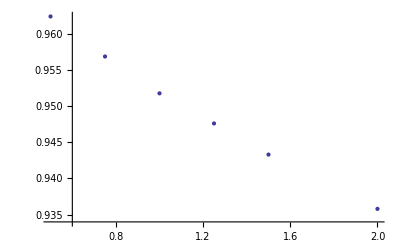

```mathematica
ListPlot[{{2,0.9358},{1.5,0.9433},{1.25,0.9476},{1,0.95176},{0.75,0.956849},{0.5,0.96238}}]
```

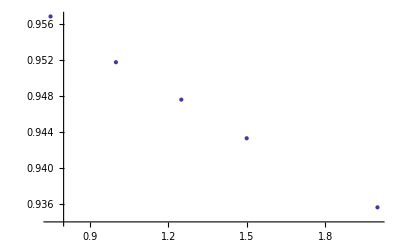

```mathematica
ListPlot[{{2,0.935616},{1.5,0.9433},{1.25,0.9476},{1,0.95176},{0.75,0.956849}}]
```

```mathematica
fit1M=FindFit[{{2,0.9358},{1.5,0.9433},{1.25,0.9476},{1,0.95176},{0.75,0.956849},{0.5,0.96238}},a + b fac,{a,b},fac]
```

{a→0.970149,b→-0.0176003}

```mathematica
fit2M=FindFit[{{2,0.9358},{1.5,0.9433},{1.25,0.9476},{1,0.95176},{0.75,0.956849},{0.5,0.96238}},a + b fac+c fac^2,{a,b,c},fac]
```

{a→0.973979,b→-0.0248955,c→0.0029181}

This uses the result of running the minimization for longer for fac = 2

```mathematica
fit2Mp=FindFit[{{2,0.935616},{1.5,0.9433},{1.25,0.9476},{1,0.95176},{0.75,0.956849},{0.5,0.96238}},a + b fac+c fac^2,{a,b,c},fac]
```

{a→0.973841,b→-0.0245626,c→0.00274286}

This uses the result of running the minimization for fac = 1 instead of using the standard GR fit

```mathematica
fit2Mpp=FindFit[{{2,0.935616},{1.5,0.9433},{1.25,0.9476},{1,0.95198},{0.75,0.956849},{0.5,0.96238}},a + b fac+c fac^2,{a,b,c},fac]
```

{a→0.973742,b→-0.0242734,c→0.00261714}

Trying a cubic fit (with the same data as fit1M and fit2M)

```mathematica
fit3M=FindFit[{{2,0.9358},{1.5,0.9433},{1.25,0.9476},{1,0.95176},{0.75,0.956849},{0.5,0.96238}},a + b fac+c fac^2+d fac^3,{a,b,c,d},fac]
```

{a→0.975957,b→-0.030942,c→0.0083007,d→-0.00143536}

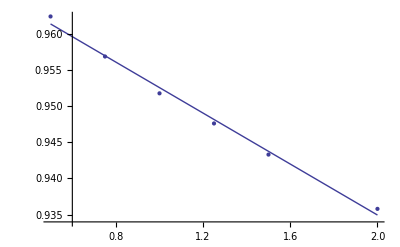

```mathematica
Show[ListPlot[{{2,0.9358},{1.5,0.9433},{1.25,0.9476},{1,0.95176},{0.75,0.956849},{0.5,0.96238}}],Plot[a+ b fac/.fit1M,{fac, 0.5,2}]]
```

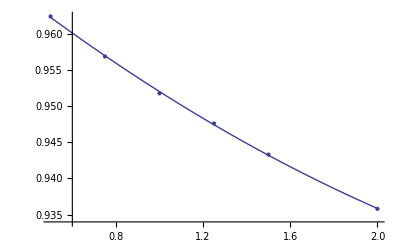

```mathematica
Show[ListPlot[{{2,0.9358},{1.5,0.9433},{1.25,0.9476},{1,0.95176},{0.75,0.956849},{0.5,0.96238}}],Plot[a+ b fac+ c fac^2/.fit2M,{fac, 0.5,2}]]
```

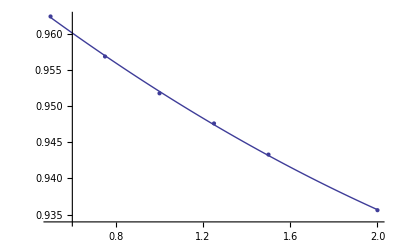

```mathematica
Show[ListPlot[{{2,0.935616},{1.5,0.9433},{1.25,0.9476},{1,0.95176},{0.75,0.956849},{0.5,0.96238}}],Plot[a+ b fac+ c fac^2/.fit2Mp,{fac, 0.5,2}]]
```

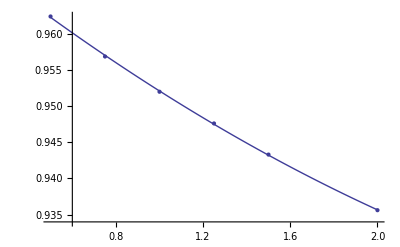

```mathematica
Show[ListPlot[{{2,0.935616},{1.5,0.9433},{1.25,0.9476},{1,0.95198},{0.75,0.956849},{0.5,0.96238}}],Plot[a+ b fac+ c fac^2/.fit2Mpp,{fac, 0.5,2}]]
```

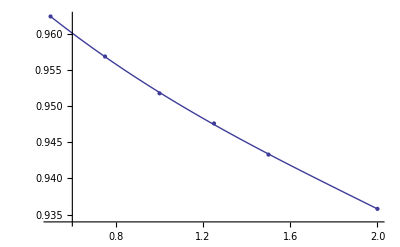

```mathematica
Show[ListPlot[{{2,0.9358},{1.5,0.9433},{1.25,0.9476},{1,0.95176},{0.75,0.956849},{0.5,0.96238}}],Plot[a+ b fac+ c fac^2+d fac^3/.fit3M,{fac, 0.5,2}]]
```

abh

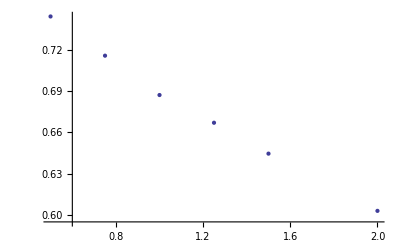

```mathematica
ListPlot[{{2,0.6030},{1.5,0.6445},{1.25,0.6669},{1,0.6870},{0.75,0.715534},{0.5,0.743972}}]
```

```mathematica
fit2a=FindFit[{{2,0.6030},{1.5,0.6445},{1.25,0.6669},{1,0.6870},{0.75,0.715534},{0.5,0.743972}},a + b fac+c fac^2,{a,b,c},fac]
```

{a→0.803577,b→-0.127707,c→0.013859}

```mathematica
fit2app=FindFit[{{2,0.6030},{1.5,0.6445},{1.25,0.6669},{1,0.690228},{0.75,0.715534},{0.5,0.743972}},a + b fac+c fac^2,{a,b,c},fac]
```

{a→0.802125,b→-0.123465,c→0.0120145}

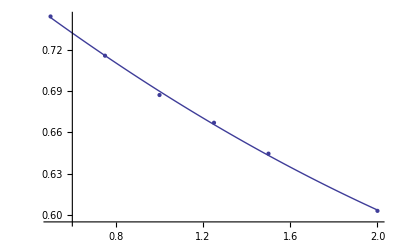

```mathematica
Show[ListPlot[{{2,0.6030},{1.5,0.6445},{1.25,0.6669},{1,0.6870},{0.75,0.715534},{0.5,0.743972}}],Plot[a+ b fac+ c fac^2/.fit2a,{fac, 0.5,2}]]
```

The consistent computation of abh for fac = 1 removes the outlier:

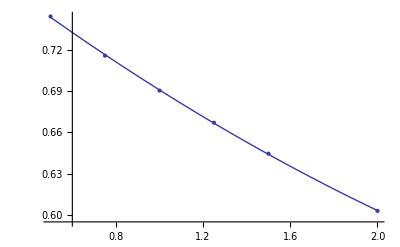

```mathematica
Show[ListPlot[{{2,0.6030},{1.5,0.6445},{1.25,0.6669},{1,0.690228},{0.75,0.715534},{0.5,0.743972}}],Plot[a+ b fac+ c fac^2/.fit2app,{fac, 0.5,2}]]
```

Jbh

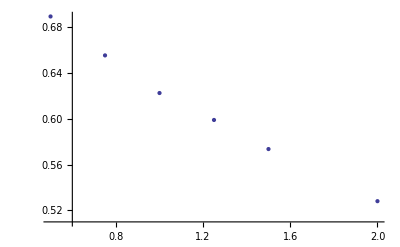

```mathematica
ListPlot[{{2,0.6030 0.9358^2},{1.5,0.6445 0.9433^2},{1.25,0.6669 0.9476^2},{1,0.6870 0.95176^2},{0.75,0.715534 0.956849^2},{0.5,0.743972 0.96238^2}}]
```

```mathematica
fit2J=FindFit[{{2,0.6030 0.9358^2},{1.5,0.6445 0.9433^2},{1.25,0.6669 0.9476^2},{1,0.6870 0.95176^2},{0.75,0.715534 0.956849^2},{0.5,0.743972 0.96238^2}},a + b fac+c fac^2,{a,b,c},fac]
```

{a→0.760785,b→-0.155181,c→0.0195762}

```mathematica
fit2Jp=FindFit[{{2,0.6030 0.9358^2},{1.5,0.6445 0.9433^2},{1.25,0.6669 0.9476^2},{1,0.690228 0.95198^2},{0.75,0.715534 0.956849^2},{0.5,0.743972 0.96238^2}},a + b fac+c fac^2,{a,b,c},fac]
```

{a→0.759339,b→-0.150958,c→0.0177401}

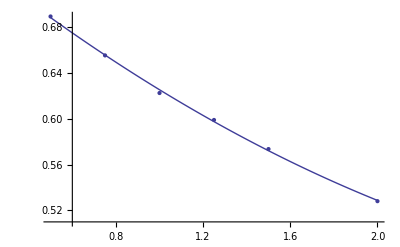

```mathematica
Show[ListPlot[{{2,0.6030 0.9358^2},{1.5,0.6445 0.9433^2},{1.25,0.6669 0.9476^2},{1,0.6870 0.95176^2},{0.75,0.715534 0.956849^2},{0.5,0.743972 0.96238^2}}],Plot[a+ b fac+ c fac^2/.fit2J,{fac, 0.5,2}]]
```

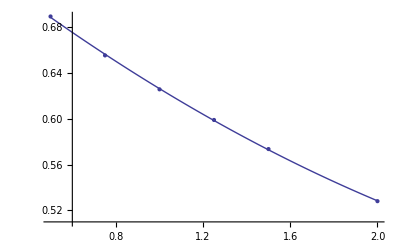

```mathematica
Show[ListPlot[{{2,0.6030 0.9358^2},{1.5,0.6445 0.9433^2},{1.25,0.6669 0.9476^2},{1,0.690228 0.95198^2},{0.75,0.715534 0.956849^2},{0.5,0.743972 0.96238^2}}],Plot[a+ b fac+ c fac^2/.fit2Jp,{fac, 0.5,2}]]
```

### Outputting Mbh and abh for other values of fac (both interpolating and extrapolating) to check

Mbh

```mathematica
a+ b fac+ c fac^2/.fit2Mpp/.fac->0.25
```

0.967837

```mathematica
a+ b fac+ c fac^2/.fit2Mpp/.fac->1.75
```

0.939278

```mathematica
a+ b fac+ c fac^2/.fit2Mpp/.fac->3
```

0.924476

```mathematica
a+ b fac+ c fac^2/.fit2Mpp
```

0.973742-0.0242734 fac+0.00261714 fac^2

abh

```mathematica
a+ b fac+ c fac^2/.fit2app/.fac->0.25
```

0.772009

```mathematica
a+ b fac+ c fac^2/.fit2app/.fac->1.75
```

0.622856

```mathematica
a+ b fac+ c fac^2/.fit2app/.fac->3
```

0.53986

```mathematica
a+ b fac+ c fac^2/.fit2app
```

0.802125-0.123465 fac+0.0120145 fac^2